```mathematica
Clear["`*"]
```

```mathematica
Options[BuffonsNeedle]={AspectRatio->0.618,Line->True};
BuffonsNeedle[r_,n_,x_:10,OptionsPattern[]]:=Block[
{y=OptionValue[AspectRatio]x,data,lines,hits,misses,mainline,needles},
data=Transpose[{Table[{ RandomReal[x],RandomReal[y]},{n}],RandomReal[π ,n]}];
lines=(Function[s,First[#]+s  r/2 Through[{Cos,Sin}[Last[#]]]]/@{1,-1})&/@data;
{misses,hits}=Map[Last,Split[Sort[Transpose[{Abs[Subtract@@(Floor/@First/@#)&/@lines],lines}]],
(First[#1]==First[#2]&)],{2}];
mainline=Line[{{#,0},{#,y}}]&/@Range[0,Ceiling[x]];
needles[color_]:=Transpose[{color,{Point/@Mean/@#,If[OptionValue[Line]===None,Nothing,Line/@#]}&/@{hits,misses}}];
Echo[StringJoin[ToString/@{
" 针长度:",TraditionalForm[r] ,
" 抛针数:", n,
" 交点数:",Length[hits],
" 估计值:",N[2n r/Length[hits]]
}]];
Show[Graphics[{mainline,If[OptionValue[Line]===None,PointSize[.005],PointSize[.01]],needles[{Red,Green}]}],AspectRatio->Automatic,ImageSize->500,Background->None] 
]/;0<=r<=1;
```

```mathematica
(*布丰投针模拟器*)
```

```mathematica
$Line=0;SeedRandom[35]
```

针长度:1/2 抛针数:500 交点数:159 估计值:3.14465

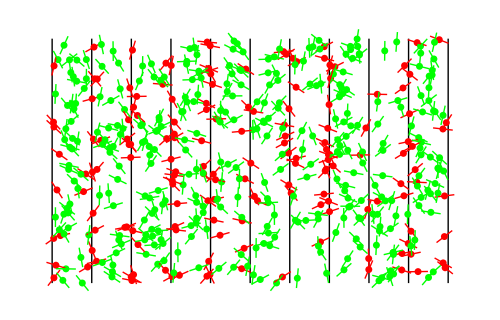

```mathematica
BuffonsNeedle[1/2,500]
```

```mathematica
$Line=1;SeedRandom[48]
```

针长度:5/6 抛针数:3408 交点数:1808 估计值:3.14159

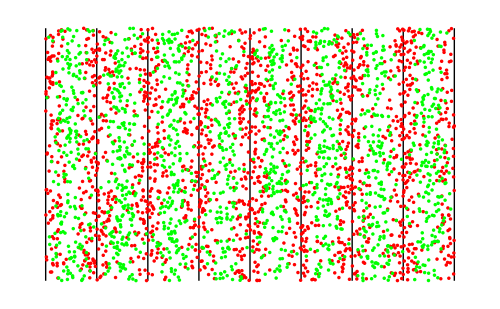

```mathematica
BuffonsNeedle[5/6,3408,8,Line->None]
```

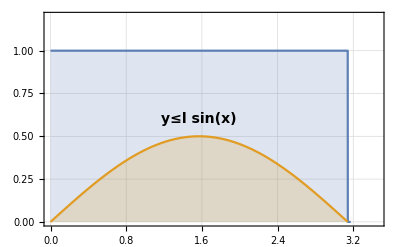

BN_3.png

```mathematica
Plot[{Piecewise[{{1,x<Pi}},0],Sin[x]/2},{x,0,1.01Pi},Filling->Axis,PlotTheme->"Detailed",
PlotRange->{{0,1.1Pi},{0,1.2}},PlotLegends->None,Exclusions->None,Epilog->Text[Style[y<=l Sin[x],Bold,FontSize->14],{Pi/2,.6}]]
Export["BN_3.png",%,Background->None]
```

```mathematica
Pi/Integrate[l Sin[x],{x,0,Pi}]
```

π/(2 l)

```mathematica
ecl[n_]:=Graphics@Array[Rotate[Circle[{0,0},{3,1}],# Pi/n]&,n];
tri=Line/@Table[{-Sin[2/3 (i+j/#) π],Cos[2/3 (i+j/#) π]},{j,1,#},{i,1,4}]&;
cir=Graphics@Table[Circle[ {Cos[#],Sin[#]}&[2 Pi (i-1)/#],1.5],{i,#}]&;
```

```mathematica
GeneralUtilities`PrintDefinitions[Sum]
```

9kwmv_shm33FrontEndObject[LinkObject["9kwmv_shm", 3, 1]]33System`Sum

```mathematica
GraphicsRow[Array[Graphics[ecl[#]]&,5]]
Show[%,ImageSize->Large]
```

-Graphics-

-Graphics-

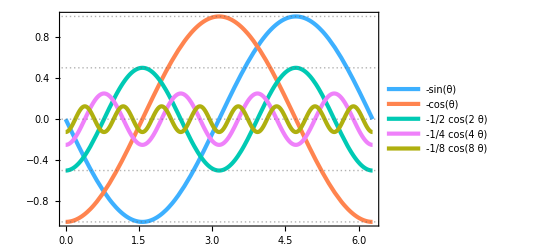

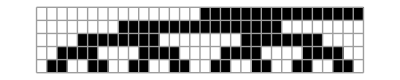

-Graphics-

{1+0.5 Sin[x],1+0.25 Sin[2 x],1+0.125 Sin[4 x],1+0.0625 Sin[8 x]}

```mathematica
grayCosines=Table[If[i==0,-Cos[θ-π/2],-(Cos[2^(i-1)θ]/2^(i-1))],{i,0,5-1}];
Plot[grayCosines,{θ,0,2 π},PlotTheme->{"Business","Detailed"},PlotStyle->96]
ArrayPlot[Transpose@Table[UnitStep/@grayCosines,{θ,2^-5/2,2π,2^-5 2π}],Mesh->True]
PolarPlot[Evaluate[1+(1/GoldenRatio)grayCosines],{θ,0,2 π},PlotTheme->{"Business","Detailed"},PlotStyle->96,Axes->False,ImageSize->Large]
```

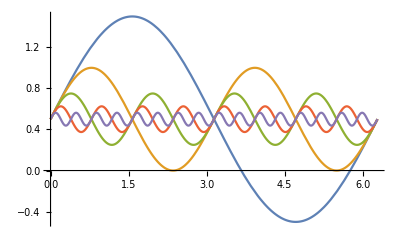

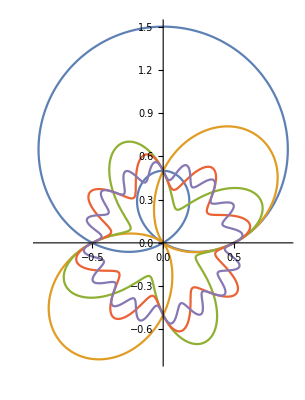

```mathematica
Plot[Evaluate[1/2+Table[Sin[2^i θ]/(2^i),{i,0,4}]],{θ,0,2 π}]
PolarPlot[Evaluate[1/2+Table[Sin[2^i θ]/(2^i),{i,0,4}]],{θ,0,2 π}]
```